```mathematica
ResourceFunction["MaTeXInstall"][]
<<MaTeX`
```

PacletObject[…]

## Classical discrete equations of motion

### Basic definitions of the quantities entering the Regge- and matter action

```mathematica
trap[s1_,s2_,H_]:=((s1+s2)/2)^2(((s1-s2)/Sqrt[2])^2-H^2);
Subscript[phi, past][s1_,s2_,H_]:=HeavisideTheta[(s1-s2)^2-4 H^2](HeavisideTheta[s1-s2]*(ArcCosh[(s1-s2)/Sqrt[(s1-s2)^2-4 H^2]]-I*Pi)-HeavisideTheta[s2-s1]*ArcCosh[(s2-s1)/Sqrt[(s1-s2)^2-4 H^2]])+HeavisideTheta[4 H^2-(s1-s2)^2](ArcSinh[(s1-s2)/Sqrt[4 H^2-(s1-s2)^2]]-I Pi/2);
Subscript[phi, fut][s1_,s2_,H_]:=HeavisideTheta[(s1-s2)^2-4 H^2](HeavisideTheta[s2-s1]*(ArcCosh[(s2-s1)/Sqrt[(s1-s2)^2-4 H^2]]-I*Pi)-HeavisideTheta[s1-s2]*ArcCosh[(s1-s2)/Sqrt[(s1-s2)^2-4 H^2]])+HeavisideTheta[4 H^2-(s1-s2)^2](ArcSinh[(s2-s1)/Sqrt[4 H^2-(s1-s2)^2]]-I Pi/2);
Subscript[theta, Lor][s1_,s2_,H_]:=-HeavisideTheta[(s1-s2)^2-4 H^2]*ArcCosh[(s1-s2)^2/((s1-s2)^2-4 H^2)]-HeavisideTheta[4 H^2-(s1-s2)^2](ArcCosh[(s1-s2)^2/(4 H^2-(s1-s2)^2)]+I*Pi);
Subscript[theta, Eucl][s1_,s2_,H_]:=ArcCos[(s1-s2)^2/(4 H^2-(s1-s2)^2)];
Subscript[S, R][s1_,s2_,H_]:=12*Sqrt[RealAbs[trap[s1,s2,H]]]*(HeavisideTheta[(s1-s2)^2-2 H^2](-I Pi/2-Subscript[theta, Lor][s1,s2,H])+HeavisideTheta[2 H^2-(s1-s2)^2](Pi/2-Subscript[theta, Eucl][s1,s2,H]))+6 s1^2(-I Pi/2-Subscript[phi, past][s1,s2,H])+6 s2^2(-I Pi/2-Subscript[phi, fut][s1,s2,H]);
Subscript[S, R,reg][s1_,s2_,H_]:=HeavisideTheta[2 H^2-(s1-s2)^2]*(12*Sqrt[Abs[trap[s1,s2,H]]]*(Pi/2-ArcCos[(s1-s2)^2/(4 H^2-(s1-s2)^2)])+6(s1^2-s2^2)ArcSinh[(s2-s1)/Sqrt[4 H^2-(s1-s2)^2]]);
Subscript[S, R,irreg1][s1_,s2_,H_]:=HeavisideTheta[(s1-s2)^2-4 H^2]*(3(s1+s2)Sqrt[(s1-s2)^2-4 H^2](-(I*Pi)/2+ArcCosh[(s1-s2)^2/((s1-s2)^2-4 H^2)])+(HeavisideTheta[s2-s1]*(-6(s1^2-s2^2)(-(I*Pi)/2+ArcCosh[(s1-s2)/Sqrt[(s1-s2)^2-4 H^2]]))+HeavisideTheta[s1-s2]*(-6(s2^2-s1^2)(-(I*Pi)/2+ArcCosh[(s2-s1)/Sqrt[(s1-s2)^2-4 H^2]]))));
Subscript[S, R,irreg2][s1_,s2_,H_]:=HeavisideTheta[4 H^2-(s1-s2)^2]*HeavisideTheta[(s1-s2)^2-2 H^2]*(3(s1+s2)Sqrt[4 H^2-(s1-s2)^2]((I*Pi)/2+ArcCosh[(s1-s2)^2/(4 H^2-(s1-s2)^2)])-6(s1^2-s2^2)ArcSinh[(s1-s2)/Sqrt[4 H^2-(s1-s2)^2]]);
w[s1_,s2_,H_]:=(s1+s2)^3/(16H);
Subscript[S, ϕ][s1_,s2_,H_,λ_,ϕ1_,ϕ2_]:=λ*w[s1,s2,H]*(ϕ1-ϕ2)^2;
Subscript[S, tot][s1_,s2_,H_,λ_,ϕ1_,ϕ2_]:=Subscript[S, R][s1,s2,H]+Subscript[S, ϕ][s1,s2,H,λ,ϕ1,ϕ2];
Subscript[dS, R][s1_,s2_,H_]:=12*D[Sqrt[RealAbs[trap[s1,s2,H]]],H]*(HeavisideTheta[(s1-s2)^2-2 H^2](-I Pi/2-Subscript[theta, Lor][s1,s2,H])+HeavisideTheta[2 H^2-(s1-s2)^2](Pi/2-Subscript[theta, Eucl][s1,s2,H]));
Subscript[dS, ϕ][s1_,s2_,H_,λ_,ϕ1_,ϕ2_]:=D[Subscript[S, ϕ][s1,s2,H,λ,ϕ1,ϕ2],H];
Subscript[dS, tot][s1_,s2_,H_,λ_,ϕ1_,ϕ2_]:=-((s1+s2)^3 λ (ϕ1-ϕ2)^2)/(16 H^2)-1/(RealAbs[(-H^2+1/2 (s1-s2)^2) (s1+s2)^2]^(3/2))6 H (-H^2+1/2 (s1-s2)^2) (s1+s2)^4 ((π/2-ArcCos[(s1-s2)^2/(4 H^2-(s1-s2)^2)]) HeavisideTheta[2 H^2-(s1-s2)^2]+(-(ⅈ π)/2+(ⅈ π+ArcCosh[(s1-s2)^2/(4 H^2-(s1-s2)^2)]) HeavisideTheta[4 H^2-(s1-s2)^2]+ArcCosh[(s1-s2)^2/(-4 H^2+(s1-s2)^2)] HeavisideTheta[-4 H^2+(s1-s2)^2]) HeavisideTheta[-2 H^2+(s1-s2)^2])
Subscript[S, E][s1_,s2_,H_,λ_,ϕ1_,ϕ2_]:=12 √(((s1+s2)/2)^2(((s1-s2)/(√2))^2+H^2))(Pi/2-ArcCos[(s1-s2)^2/(4 H^2+(s1-s2)^2)])+6(s1^2-s2^2)(Pi/2-ArcCos[(s2-s1)/(√(4 H^2+(s1-s2)^2))])+λ*(s1+s2)^3/(16H)(ϕ1-ϕ2)^2
Subscript[dS, E][s1_,s2_,H_,λ_,ϕ1_,ϕ2_]:=12(H (s1+s2)^2)/(2 √((H^2+1/2 (s1-s2)^2) (s1+s2)^2))(Pi/2-ArcCos[(s1-s2)^2/(4 H^2+(s1-s2)^2)])-λ*(s1+s2)^3/(16 H^2)(ϕ1-ϕ2)^2
Subscript[S, Λ][s1_,s2_,H_,Λ_]:=Λ/4(s1^2+s2^2)*(s1+s2)^2*H
```

We should check that the Schaefli identity is satisfied for the different regions

```mathematica
Simplify[Subscript[S, R,irreg1][s1,s2,H],0<H^2<1/4(s1-s2)^2&&s1>0&&s2>0&&H>0&&s1<s2]
Simplify[Subscript[S, R,irreg1][s1,s2,H],0<H^2<1/4(s1-s2)^2&&s1>0&&s2>0&&H>0&&s1>s2]
Simplify[Subscript[S, R,irreg2][s1,s2,H],1/4(s1-s2)^2<H^2<1/2(s1-s2)^2&&s1>0&&s2>0&&H>0]
Simplify[Subscript[S, R][s1,s2,H],H^2>1/2(s1-s2)^2&&s1>0&&s2>0&&H>0&&s1<s2]
```

3 ⅈ (s1^2-s2^2) (π+2 ⅈ ArcCosh[(s1-s2)/(√(-4 H^2+(s1-s2)^2))])+3 √(-4 H^2+(s1-s2)^2) (s1+s2) (-(ⅈ π)/2+ArcCosh[(s1-s2)^2/(-4 H^2+(s1-s2)^2)])

3 √(-4 H^2+(s1-s2)^2) (s1+s2) (-(ⅈ π)/2+ArcCosh[(s1-s2)^2/(-4 H^2+(s1-s2)^2)])+3 (s1^2-s2^2) (-ⅈ π+2 ArcCosh[(-s1+s2)/(√(-4 H^2+(s1-s2)^2))])

3 √(4 H^2-(s1-s2)^2) (s1+s2) ((ⅈ π)/2+ArcCosh[(s1-s2)^2/(4 H^2-(s1-s2)^2)])-6 (s1^2-s2^2) ArcSinh[(s1-s2)/(√(4 H^2-(s1-s2)^2))]

3 √(H^2-1/2 (s1-s2)^2) (s1+s2) (π-2 ArcCos[(s1-s2)^2/(4 H^2-(s1-s2)^2)])-6 s1^2 ArcSinh[(s1-s2)/(√(4 H^2-(s1-s2)^2))]-6 s2^2 ArcSinh[(-s1+s2)/(√(4 H^2-(s1-s2)^2))]

```mathematica
Simplify[D[Sqrt[RealAbs[trap[s1,s2,H]]],s1],H^2>1/2(s1-s2)^2&&s1>0&&s2>0&&H>0]
```

(H^2+s1 (-s1+s2))/(√(4 H^2-2 (s1-s2)^2))

Check the Schlaefli condition for the regular action, 1/2(s1-s2)^2<H^2

```mathematica
Simplify[3 √(H^2-1/2 (s1-s2)^2) (s1+s2) D[(π-2 ArcCos[(s1-s2)^2/(4 H^2-(s1-s2)^2)]),H]+6 (s1^2-s2^2) D[ArcSinh[(-s1+s2)/(√(4 H^2-(s1-s2)^2))],H],H>0&&s1>0&&s2>0&&1/2(s1-s2)^2<H^2]
Simplify[3 √(H^2-1/2 (s1-s2)^2) (s1+s2) D[(π-2 ArcCos[(s1-s2)^2/(4 H^2-(s1-s2)^2)]),s1]+6 (s1^2-s2^2) D[ArcSinh[(-s1+s2)/(√(4 H^2-(s1-s2)^2))],s1],H>0&&s1>0&&s2>0&&1/2(s1-s2)^2<H^2]
```

0

```mathematica
0Simplify[D[(Pi/2-ArcCos[(s2-s1)/(√(4 H^2+(s1-s2)^2))]),H],H>0&&s1>0&&s2>0]
```

Check the condition for the intermediate regime 1/4(s1-s2)^2<H^2<1/2(s1-s2)^2:

```mathematica
Simplify[6 √(1/2(s1-s2)^2-H^2) (s1+s2) D[((ⅈ π)/2+ArcCosh[(s1-s2)^2/(4 H^2-(s1-s2)^2)]),H]-6 (s1^2-s2^2) D[ArcSinh[(s1-s2)/(√(4 H^2-(s1-s2)^2))],H],H>0&&s1>0&&s2>0&&1/4(s1-s2)^2<H^2<1/2(s1-s2)^2]
Simplify[6 √(1/2(s1-s2)^2-H^2) (s1+s2) D[((ⅈ π)/2+ArcCosh[(s1-s2)^2/(4 H^2-(s1-s2)^2)]),s1]-6 (s1^2-s2^2) D[ArcSinh[(s1-s2)/(√(4 H^2-(s1-s2)^2))],s1],H>0&&s1>0&&s2>0&&1/4(s1-s2)^2<H^2<1/2(s1-s2)^2]
```

```mathematica
0{{0,6},{-6000,6000}}
```

0

Check the condition for the regime 0 <H^2<1/4(s1-s2)^2:

```mathematica
Simplify[6(s1^2-s2^2) D[((I*π)/2+ ArcCosh[(s1-s2)/(√(-4 H^2+(s1-s2)^2))]),H]+6 √(-H^2+1/2(s1-s2)^2) (s1+s2) D[(-(ⅈ π)/2+ArcCosh[(s1-s2)^2/(-4 H^2+(s1-s2)^2)]),H],0<H^2<1/4(s1-s2)^2&&s1>0&&s2>0&&H>0&&s1<s2]
Simplify[6(s1^2-s2^2) D[((I*π)/2+ ArcCosh[(s1-s2)/(√(-4 H^2+(s1-s2)^2))]),s1]+6tion-first attempted in 198 √(-H^2+1/2(s1-s2)^2) (s1+s2) D[(-(ⅈ π)/2+ArcCosh[(s1-s2)^2/(-4 H^2+(s1-s2)^2)]),s1],0<H^2<1/4(s1-s2)^2&&s1>0&&s2>0&&H>0&&s1<s2]
```

0

0

```mathematica
Simplify[D[(Pi/2-ArcCos[(s2-s1)/(√(4 H^2+(s1-s2)^2))]),H],H>0&&s1>0&&s2>0]
```

Check the Schläfli identity for Euclidean action

```mathematica
Simplify[12 √(((s1+s2)/2)^2(((s1-s2)/(√2))^2+H^2))D[(Pi/2-ArcCos[(s1-s2)^2/(4 H^2+(s1-s2)^2)]),H]+6(s1^2-s2^2)D[(Pi/2-ArcCos[(s2-s1)/(√(4 H^2+(s1-s2)^2))]),H],H>0&&s1>0&&s2>0]
```

0

The Schlaefli identities are satisfied!

```mathematica
Subscript[S, R][10,20,51]-Subscript[S, Λ][10,20,53,0.5]
```

-2.98134×10^6

```mathematica
Table[N[Subscript[S, R][10,20,H]-Subscript[S, Λ][10,20,H,Λ]],{H,20,1000}]
```

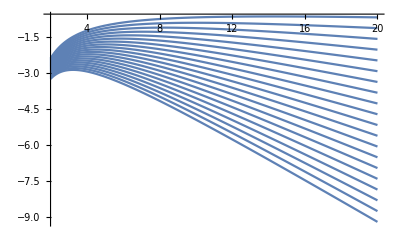

```mathematica
Show[Array[Plot[N[Subscript[S, R,reg][1,2,H]-Subscript[S, Λ][1,2,H,0.002#]],{H,2,20},PlotRange->All]&,20],PlotLegends->Automatic,PlotStyle->ColorData["DeepSeaColors"]/@{0.1,0.2,0.3}]
```

### Plots of the Regge action and its derivative

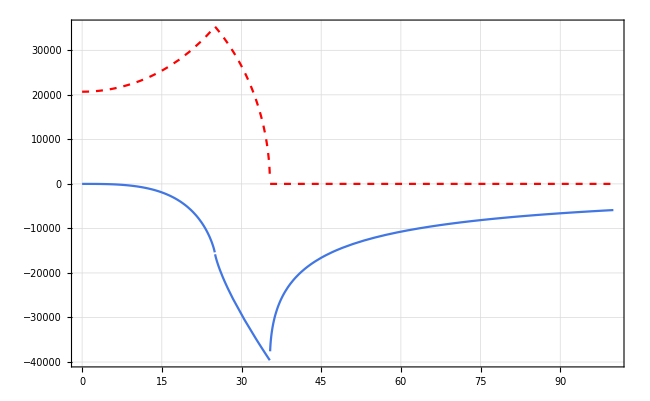

```mathematica
VacReggePlot=ReImPlot[Evaluate@Table[Subscript[S, R][50,d,H],{d,100,100}],{H,0,100}, PlotRange->Full,Frame->True,GridLines->Automatic,FrameLabel->{{Style[MaTeX["S_{\mathrm{R}}", Magnification->3],FontSize->16],},{Style[MaTeX["H",Magnification->3],FontSize->16],}},PlotStyle->ColorData["DeepSeaColors"]/@{0.6},ImageSize->650,FrameTicksStyle->Directive[FontSize->16],ReImStyle->{,{Red,Dashed}}]
Export["/ssd/ri47hud/Projects/Spin Foam Cosmology/plots/VacReggePlot.pdf",VacReggePlot];
```

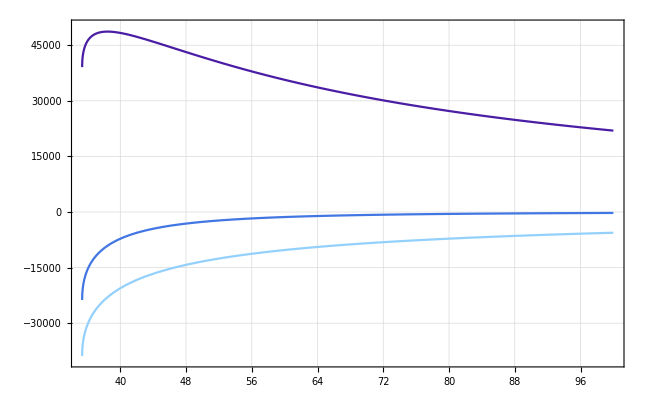

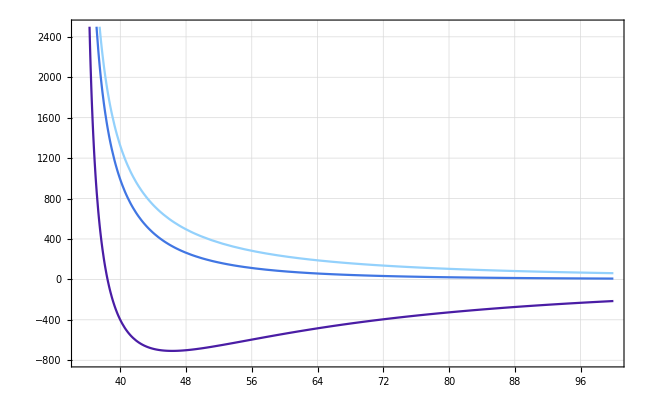

```mathematica
MatterReggePlot1=Plot[Evaluate@Table[Subscript[S, tot][50,100,H,1,0,2*f+2 √(2/3)],{f,-1,1}],{H,Sqrt[1250],100}, PlotRange->{{Sqrt[1250],100},{-40000,50000}},Frame->True,GridLines->Automatic,FrameLabel->{{Style[MaTeX["S_{\mathrm{tot}}", Magnification->3],FontSize->16],},{Style[MaTeX["H",Magnification->3],FontSize->16],}},PlotStyle->ColorData["DeepSeaColors"]/@{0.9,0.6,0.3},ImageSize->650,FrameTicksStyle->Directive[FontSize->16]]
MatterReggePlot2=Plot[Evaluate@Table[Subscript[dS, tot][50,100,H,1,0,2*f+2 √(2/3)],{f,-1,1}],{H,Sqrt[1250],100}, PlotRange->{{Sqrt[1250],100},{-800,2500}},Frame->True,GridLines->Automatic,FrameLabel->{{Style[MaTeX["\partial S_{\mathrm{tot}}/\partial H", Magnification->3],FontSize->16],},{Style[MaTeX["H",Magnification->3],FontSize->16],}},PlotStyle->ColorData["DeepSeaColors"]/@{0.9,0.6,0.3},ImageSize->650,FrameTicksStyle->Directive[FontSize->16]]
Export["/ssd/ri47hud/Projects/Spin Foam Cosmology/plots/MatterReggePlot1.pdf",MatterReggePlot1];
Export["/ssd/ri47hud/Projects/Spin Foam Cosmology/plots/MatterReggePlot2.pdf",MatterReggePlot2];
```

Let’s plot the total action and its derivative w.r.t. H

```mathematica
Sqrt[1250]
```

25 √2

```mathematica
Manipulate[ReImPlot[Subscript[S, tot][50,100,H,1,0,2*f+2 √(2/3)],{H,Sqrt[1250],100},PlotRange->{{Sqrt[1250],100},Full}],{f,-1,1}]
```

```mathematica
Manipulate[ReImPlot[Subscript[dS, tot][50,100,H,1,0,f],{H,Sqrt[1250],100},PlotRange->{{Sqrt[1250],100},{-800,2500}}],{f,0,10}]
```

```mathematica
Manipulate[ReImPlot[Subscript[dS, tot][50,100,H,-1,0,f],{H,1,100},PlotRange->{{1,100},{-20000,20000}}],{f,0,10}]
```

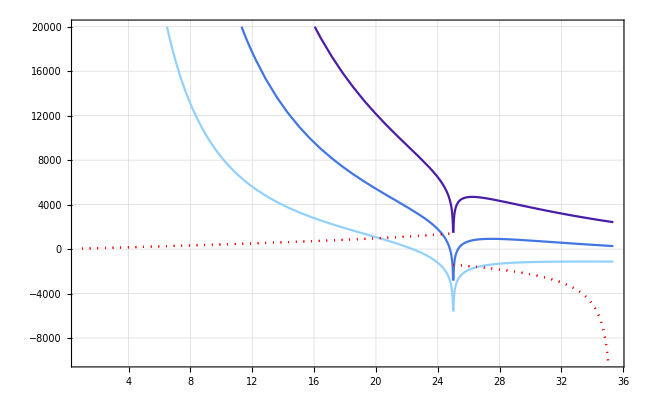

/ssd/ri47hud/Projects/Spin Foam Cosmology/plots/dReggePlotIandII.pdf

```mathematica
dReggeIandII=ReImPlot[Evaluate@Table[Subscript[dS, tot][50,100,H,-1,0,d],{d,{2,3.5,5}}],{H,1,Sqrt[1250]}, PlotRange->{{1,Sqrt[1250]},{-10000,20000}},Frame->True,GridLines->Automatic,FrameLabel->{{Style[MaTeX["\partial S_{\mathrm{tot}}^{\mathrm{L},+}/\partial R", Magnification->3],FontSize->16],},{Style[MaTeX["R",Magnification->3],FontSize->16],}},PlotStyle->ColorData["DeepSeaColors"]/@{0.9,0.6,0.3},ImageSize->650,FrameTicksStyle->Directive[FontSize->16],PlotLegends->{MaTeX["\mathfrak{Re},\;\Delta\phi = 2",Magnification->2],MaTeX["\mathfrak{Re},\;\Delta\phi = 3.5",Magnification->2],MaTeX["\mathfrak{Re},\;\Delta\phi = 5", Magnification->2]},ReImStyle->{,Red}]
Export["/ssd/ri47hud/Projects/Spin Foam Cosmology/plots/dReggePlotIandII.pdf",dReggeIandII]
```

```mathematica
Manipulate[ReImPlot[Subscript[S, E][50,100,H,λ,0,2 √(2/3)],{H,0.1,100},PlotRange->Full],{λ,-2,2}]
```

```mathematica
Manipulate[ReImPlot[Subscript[dS, E][50,100,H,λ,0,2 √(2/3)],{H,0.1,100},PlotRange->Full],{λ,-2,2}]
```

```mathematica
Manipulate[ReImPlot[Subscript[S, E][50,100,H,λ,0,2 √(2/3)]+4Pi*12*√((150/2)^2((50/(√2))^2+H^2)),{H,√(50^2/4),√(50^2/2)},PlotRange->{{√(50^2/4),√(50^2/2)},{-1000,1000000}}],{λ,-2,2}]
```

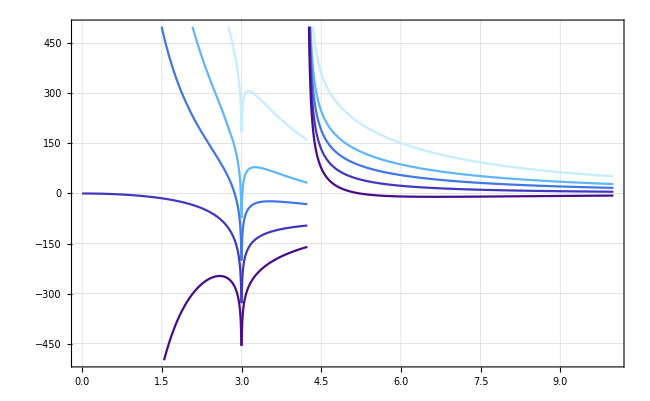

```mathematica
dReggePlotLambda=Plot[Evaluate@Table[Re[Subscript[dS, tot][1,7,H,λ,0,30]],{λ,{-0.16,-0.08,-0.04,0,0.04}}],{H,0,10}, PlotRange->{{0,10},{-500,500}},Frame->True,GridLines->Automatic,FrameLabel->{{Style[MaTeX["\mathfrak{Re}[\partial S_{\mathrm{tot}}/\partial H]", Magnification->2],FontSize->16],},{Style[MaTeX["H",Magnification->2],FontSize->16],}},PlotStyle->ColorData["DeepSeaColors"]/@{1.0,0.8,0.6,0.4,0.2},ImageSize->650,FrameTicksStyle->Directive[FontSize->16],PlotLegends->{MaTeX["\lambda = -0.16",Magnification->2],MaTeX["\lambda = -0.08",Magnification->2],MaTeX["\lambda = -0.04", Magnification->2],MaTeX["\lambda = 0", Magnification->2],MaTeX["\lambda = 0.04", Magnification->2]}]
Export["/ssd/ri47hud/Projects/Spin Foam Cosmology/plots/dReggePlotLambda.pdf",dReggePlotLambda];
```

```mathematica
ComplexPlot3D[Log[z],{z,10}]
```

-Graphics3D-

```mathematica
ComplexPlot3D[Sqrt[z],{z,10}]
```

-Graphics3D-

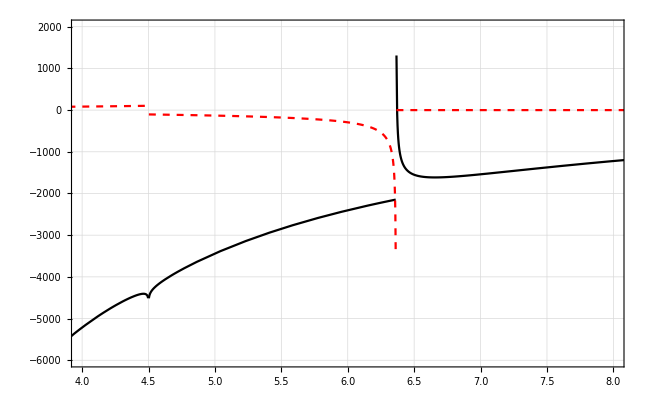

```mathematica
dReggePlot=ReImPlot[Subscript[dS, tot][1,10,H,0.1,1,100],{H,1,10}, PlotRange->{{4,8},{-6000,2000}},Frame->True,GridLines->Automatic,FrameLabel->{{Style[MaTeX["\partial S_{\mathrm{tot}}/\partial H", Magnification->2],FontSize->16],},{Style[MaTeX["H",Magnification->2],FontSize->16],}},PlotStyle->{Black},ImageSize->650,FrameTicksStyle->Directive[FontSize->16],ReImStyle->{Black,{Red,Dashed}}]
Export["/ssd/ri47hud/Projects/Spin Foam Cosmology/plots/dReggePlot.pdf",dReggePlot];
```

We impose the causality conditions such that k^2<0, where k[a,b,t]\equiv Sqrt[Abs[k^2]] and t^2=Abs[t^2]. The variables a,b are the spatial edge lengths. Notice that in the length formulation as defined below, the condition that the edge is timelike is automatically encoded by assuming that t^2>0.

```mathematica
k[a_,b_,t_]:=((a+b)/4)*Sqrt[4t^2+(a-b)^2];
ldual[a_,b_,t_]:=Sqrt[((a+b)/2)^2*((3(a-b)^2+4t^2)/(2(a-b)^2+4t^2))];
Vdual[a_,b_,t_]:=(ldual[a,b,t]^3*t)/4;
w[a_,b_,t_]:=Vdual[a,b,t]/(t^2);
ratio[a_,b_,t_]:=(a^2-b^2)^2/(16*Abs[k[a,b,t]^2]);
defk[a_,b_,t_]:=ArcCos[(a-b)^2/(2(a-b)^2+4t^2)];
defj[a_,b_,t_]:=ArcSinh[(b-a)/(Sqrt[2(a-b)^2+4t^2])];
SLRC[a_,b_,t_]:=12*k[a,b,t]*(Pi/2-defk[a,b,t])+6(a^2-b^2)*defj[a,b,t]
SMatter[a_,b_,t_,λ_,ϕ0_,ϕ1_]:=λ*w[a,b,t]*(ϕ1-ϕ0)^2
dSLRCdt[a_,b_,t_]:=12*(√((a+b)^2) t)/(√((a-b)^2+4 t^2))*(Pi/2-defk[a,b,t]);
dSMatterdt[a_,b_,t_,λ_,ϕ0_,ϕ1_]:=-((a+b)^3 √(3/2 (a-b)^2+2 t^2) (3 (a-b)^4+16 (a-b)^2 t^2+8 t^4) λ (ϕ0-ϕ1)^2)/(64 t^2 ((a-b)^2+2 t^2)^(5/2));
Stot[a_,b_,t_,λ_,ϕ0_,ϕ1_]:=SLRC[a,b,t]+SMatter[a,b,t,λ,ϕ0,ϕ1];
dStotdt[a_,b_,t_,λ_,ϕ0_,ϕ1_]:=dSLRCdt[a,b,t]+dSMatterdt[a,b,t,λ,ϕ0,ϕ1];
```

Let’s plot the length Regge action without matter

```mathematica
Manipulate[Plot[SLRC[1,Sqrt[1+d],t],{t,0,100}],{d,0,10}]
```

Clearly, the only classical solution is the flat one with a=b. This is in accordance with the continuum result. For this solution, there is an invariance w.r.t. the timelike edge length.

What happens if we add matter?

```mathematica
Manipulate[Plot[Stot[1,1+ds,t,10^logλ,1,1+dϕ],{t,0,10}],{ds,1,10},{logλ,-3,0},{dϕ,1,10}]
Manipulate[Plot[dStotdt[0,ds,t,1,0,dϕ],{t,0,10}],{ds,0,10},{dϕ,0,10}]
solt[λ_,dϕ_,ds_]:=Sqrt[(9/(32*8)*λ*ds^2*dϕ^2)/(3/2-λ*dϕ^2/32)]
```

We obtain classical solutions for the coupled system which depD[k[s1,s2,t1],s1]*1/(D[k[s1,s2,t1],t1])
(√((s1-s2)^2+4 t1^2) (((s1-s2) (s1+s2))/(4 √((s1-s2)^2+4 t1^2))+1/4 √((s1-s2)^2+4 t1^2)))/((s1+s2) t1)ends on λ and the difference of boundary scalar fields.

### Conditions for the existence of solutions

Let’s try to find explicit solutions:

```mathematica
tfit[d_,a_,b_]:=a*d^(b)
```

```mathematica
tsol=Array[{#,t/.FindRoot[dStotdt[0,#,t,1,0 ,1/#]==0,{t,0.5}]}&,999,{2,1000}];
FindFit[tsol,tfit[d,a,b],{a,b},d]
```

{a→0.209259,b→0.333187}

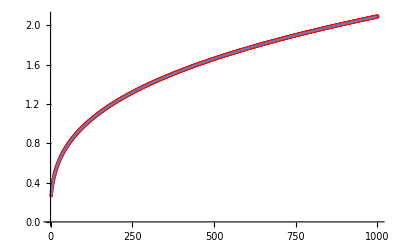

```mathematica
Show[ListPlot[tsol,PlotStyle->Red],Plot[tfit[d,a,b]/.{a->0.20925901975764638,b->0.3331871190973599},{d,2,1000}]]
```

For ds = 1/dϕ, solutions for the equations of motion are roughly given by t~ds^(1/3)

Keeping ds or dϕ fixed, what happens if the non-fixed variable is increased?

```mathematica
Manipulate[Plot[dStotdt[0,1,t,1,0,dϕ],{t,0,10}],{dϕ,0,10}]
```

For fixed s, solutions t grow very fast with increasing dϕ .

```mathematica
Manipulate[Plot[dStotdt[0,ds,t,1,0,1],{t,0,10}],{ds,0,10}]
```

```mathematica
0.2909695*5^(3/2)
```

3.25314

```mathematica
dStotdt[0,ds,t,1,0,1/ds^(3/2)]
```

```mathematica
Simplify[-(√((3 ds^2)/2+2 t^2) (3 ds^4+16 ds^2 t^2+8 t^4))/(64 t^2 (ds^2+2 t^2)^(5/2))+(12 √(ds^2) t (π/2-ArcCos[ds^2/(2 ds^2+4 t^2)]))/(√(ds^2+4 t^2)),Assumptions->Element[{ds,t},Reals]]
```

```mathematica
Solve[-(√((3 ds^2)/2+2 t^2) (3 ds^4+16 ds^2 t^2+8 t^4))/(64 t^2 (ds^2+2 t^2)^(5/2))+(6 t ds(π-2 ArcCos[ds^2/(2 ds^2+4 t^2)]))/(√(D[k[s1,s2,t1],s1]*1/(D[k[s1,s2,t1],t1])
(√((s1-s2)^2+4 t1^2) (((s1-s2) (s1+s2))/(4 √((s1-s2)^2+4 t1^2))+1/4 √((s1-s2)^2+4 t1^2)))/((s1+s2) t1)D[k[s1,s2,t1],s1]*1/(D[k[s1,s2,t1],t1])
(√((s1-s2)^2+4 t1^2) (((s1-s2) (s1+s2))/(4 √((s1-s2)^2+4 t1^2))+1/4 √((s1-s2)^2+4 t1^2)))/((s1+s2) t1)D[k[s1,s2,t1],s1]*1/(D[k[s1,s2,t1],t1])
(√((s1-s2)^2+4 t1^2) (((s1-s2) (s1+s2))/(4 √((s1-s2)^2+4 t1^2))+1/4 √((s1-s2)^2+4 t1^2)))/((s1+s2) t1)ds^2+4 t^2))==0,t]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[-(√((3 ds^2)/2+2 t^2) (3 ds^4+16 ds^2 t^2+8 t^4))/(64 t^2 (ds^2+2 t^2)^(5/2))+(6 ds t (π-2 ArcCos[ds^2/(2 ds^2+4 t^2)]))/(√(ds^2+4 t^2))==0,t]

```mathematica
Manipulate[Plot[dStotdt[0,ds,t,1,0,1],{t,0,10},PlotRange->{{0,1},{-1,1}}],{ds,1,10}]
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

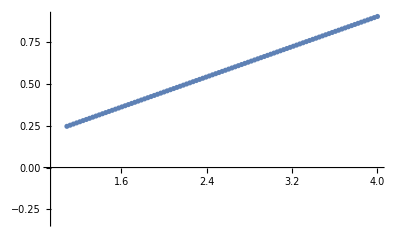

{a→0.,b→4.62031}

```mathematica
tsol2=Array[{#,t/.FindRoot[dStotdt[0,#,t,1,0,1]==0,{t,0.5}]}&,100,{1,4}];
ListPlot[tsol2]
(*tsoljoined=Join[tsol2,tsol3];*)
tfit2[dϕ_,a_,b_]:=0.209695*dϕ^(2/3)+a*dϕ*Exp[dϕ*b];
FindFit[tsol2,{tfit2[dϕ,a,b],a>0,b>0},{{a,1},{b,3}},dϕ]
```

```mathematica
Show[ListPlot[tsoljoined,PlotStyle->Red],Plot[tfit2[dϕ,a,b]/.{a->1.886981616361221*^-7,b->2.5588822462178418},{dϕ,2,6.9}]]
```

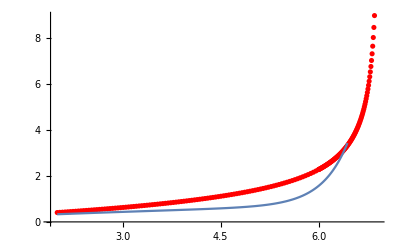
```mathematica
-Graphics--Graphics-
```

### Equations for a bulk time step

```mathematica
D[SMatter[s1,s2,t1,λ,ϕ1,ϕ2],s1]
```

(3 √(((s1+s2)^2 (3 (s1-s2)^2+4 t1^2))/(2 (s1-s2)^2+4 t1^2)) ((6 (s1-s2) (s1+s2)^2)/(2 (s1-s2)^2+4 t1^2)-(4 (s1-s2) (s1+s2)^2 (3 (s1-s2)^2+4 t1^2))/((2 (s1-s2)^2+4 t1^2)^2)+(2 (s1+s2) (3 (s1-s2)^2+4 t1^2))/(2 (s1-s2)^2+4 t1^2)) λ (-ϕ1+ϕ2)^2)/(64 t1)

```mathematica
S2slice[s0_,s1_,s2_,t0_,t1_,λ_,ϕ0_,ϕ1_,ϕ2_]:=Stot[s0,s1,t0,λ,ϕ0,ϕ1]+Stot[s1,s2,t1,λ,ϕ1,ϕ2];
solϕ[s0_,s1_,s2_,t0_,t1_,ϕ0_,ϕ2_]:=(w[s0,s1,t0]ϕ0+w[s1,s2,t1]ϕ2)/(w[s0,s1,t0]+w[s1,s2,t1]);
dS2sliceds[s0_,s1_,s2_,t0_,t1_,λ_,ϕ0_,ϕ1_,ϕ2_]:=12*(-((s0-s1) (s0+s1))/(4 √((s0-s1)^2+4 t0^2))+1/4 √((s0-s1)^2+4 t0^2))*(Pi/2-defk[s0,s1,t0])-12s1*defj[s0,s1,t0]+12*(((s1-s2) (s1+s2))/(4 √((s1-s2)^2+4 t1^2))+1/4 √((s1-s2)^2+4 t1^2))*(Pi/2-defk[s1,s2,t1])+12s1*defj[s1,s2,t1]+(3 √(((s0+s1)^2 (3 (s0-s1)^2+4 t0^2))/(2 (s0-s1)^2+4 t0^2)) (-(6 (s0-s1) (s0+s1)^2)/(2 (s0-s1)^2+4 t0^2)+(4 (s0-s1) (s0+s1)^2 (3 (s0-s1)^2+4 t0^2))/((2 (s0-s1)^2+4 t0^2)^2)+(2 (s0+s1) (3 (s0-s1)^2+4 t0^2))/(2 (s0-s1)^2+4 t0^2)) λ (-ϕ0+ϕ1)^2)/(64 t0)+(3 √(((s1+s2)^2 (3 (s1-s2)^2+4 t1^2))/(2 (s1-s2)^2+4 t1^2)) ((6 (s1-s2) (s1+s2)^2)/(2 (s1-s2)^2+4 t1^2)-(4 (s1-s2) (s1+s2)^2 (3 (s1-s2)^2+4 t1^2))/((2 (s1-s2)^2+4 t1^2)^2)+(2 (s1+s2) (3 (s1-s2)^2+4 t1^2))/(2 (s1-s2)^2+4 t1^2)) λ (-ϕ1+ϕ2)^2)/(64 t1);
```

```mathematica
Manipulate[Plot[dS2sliceds[0,s1,Δs,t0,t1,1,0,solϕ[0,s1,Δs,t0,t1,0,Δϕ],Δϕ],{s1,0,10}],{Δs,0,10},{t0,0,10},{t1,0,10},{Δϕ,0,10}]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
dS2sliceds[s0,s1,s2,t0,t1,1,ϕ0,solϕ[s0,s1,s2,t0,t1,ϕ0,ϕ2],ϕ2]
```

```mathematica
D[SMatter[s0,s1,t0,λ,ϕ0,ϕ1],s1];
D[SMatter[s0,s1,t0,λ,ϕ0,ϕ1],t0];
SMatter[s0,s1,t0,λ,ϕ0,ϕ1];
Simplify[D[k[s0,s1,t0],s1]]
k[s0,s1,t0]
w[s0,s1,t0]
defj[s0,s1,t0]
defk[s0,s1,t0]
Series[ArcCos[1/(4*c^2/x^2-1)],{x,0,4}]
```

(-s0 s1+s1^2+2 t0^2)/(2 √(s0^2-2 s0 s1+s1^2+4 t0^2))

1/4 (s0+s1) √((s0-s1)^2+4 t0^2)

((((s0+s1)^2 (3 (s0-s1)^2+4 t0^2))/(2 (s0-s1)^2+4 t0^2))^(3/2))/(32 t0)

ArcSinh[(-s0+s1)/(√(2 (s0-s1)^2+4 t0^2))]

ArcCos[(s0-s1)^2/(2 (s0-s1)^2+4 t0^2)]

π/2-x^2/(4 c^2)-x^4/(16 c^4)+O[x]^5

```mathematica
D[((s0+s1)^2 (3 (s0-s1)^2+4 t0^2))/(2 (s0-s1)^2+4 t0^2),t0]
```

(8 (s0+s1)^2 t0)/(2 (s0-s1)^2+4 t0^2)-(8 (s0+s1)^2 t0 (3 (s0-s1)^2+4 t0^2))/((2 (s0-s1)^2+4 t0^2)^2)

```mathematica
Simplify[(8 (s0+s1)^2 t0)/(2 (s0-s1)^2+4 t0^2)-(8 (s0+s1)^2 t0 (3 (s0-s1)^2+4 t0^2))/((2 (s0-s1)^2+4 t0^2)^2)]
```

-(2 (s0-s1)^2 (s0+s1)^2 t0)/((s0^2-2 s0 s1+s1^2+2 t0^2)^2)

```mathematica
TrigToExp[ArcSinh[(-s0+s1)/(√(2 (s0-s1)^2+4 t0^2))]]
```

Log[(-s0+s1)/(√(2 (s0-s1)^2+4 t0^2))+√(1+(-s0+s1)^2/(2 (s0-s1)^2+4 t0^2))]

```mathematica
D[((s0+s1)^2 (3 (s0-s1)^2+4 t0^2))/(2 (s0-s1)^2+4 t0^2),s1]
```

-(6 (s0-s1) (s0+s1)^2)/(2 (s0-s1)^2+4 t0^2)+(4 (s0-s1) (s0+s1)^2 (3 (s0-s1)^2+4 t0^2))/((2 (s0-s1)^2+4 t0^2)^2)+(2 (s0+s1) (3 (s0-s1)^2+4 t0^2))/(2 (s0-s1)^2+4 t0^2)

```mathematica
Simplify[-(6 (s0-s1) (s0+s1)^2)/(2 (s0-s1)^2+4 t0^2)+(4 (s0-s1) (s0+s1)^2 (3 (s0-s1)^2+4 t0^2))/((2 (s0-s1)^2+4 t0^2)^2)+(2 (s0+s1) (3 (s0-s1)^2+4 t0^2))/(2 (s0-s1)^2+4 t0^2)]
```

((s0+s1) (3 s0^4-12 s0^3 s1+3 s1^4+12 s1^2 t0^2+8 t0^4+2 s0^2 (9 s1^2+4 t0^2)-4 s0 (3 s1^3+5 s1 t0^2)))/((s0^2-2 s0 s1+s1^2+2 t0^2)^2)

```mathematica
Numerator[((s0+s1) (3 s0^4-12 s0^3 s1+3 s1^4+12 s1^2 t0^2+8 t0^4+2 s0^2 (9 s1^2+4 t0^2)-4 s0 (3 s1^3+5 s1 t0^2)))/((s0^2-2 s0 s1+s1^2+2 t0^2)^2)]
```

(s0+s1) (3 s0^4-12 s0^3 s1+3 s1^4+12 s1^2 t0^2+8 t0^4+2 s0^2 (9 s1^2+4 t0^2)-4 s0 (3 s1^3+5 s1 t0^2))

```mathematica
FullSimplify[(s0+s1) (3 s0^4-12 s0^3 s1+3 s1^4+12 s1^2 t0^2+8 t0^4+2 s0^2 (9 s1^2+4 t0^2)-4 s0 (3 s1^3+5 s1 t0^2)),Assumptions->Element[{s0,s1,t0},Reals]]
```

(s0+s1) (3 (s0-s1)^4+4 (2 s0-3 s1) (s0-s1) t0^2+8 t0^4)

```mathematica
Factor[(s0+s1) (3 (s0-s1)^4+4 (2 s0-3 s1) (s0-s1) t0^2+8 t0^4)]
```

```mathematica
(s0+s1) (3 s0^4-12 s0^3 s1+18 s0^2 s1^2-12 s0 s1^3+1/Sqrt[2x^2+4]3 s1^4+8 s0^2 t0^2-20 s0 s1 t0^2+12 s1^2 t0^2+8 t0^4)
```

```mathematica
3/2*((s0+s1) (3 (s0-s1)^4+4 (2 s0-3 s1) (s0-s1) t0^2+8 t0^4)/(s0^2-2 s0 s1+s1^2+2 t0^2)^2)/(((s0+s1)^2 (3 (s0-s1)^2+4 t0^2))/(2 (s0-s1)^2+4 t0^2))
```

```mathematica
FullSimplify[(3 (2 (s0-s1)^2+4 t0^2) (3 (s0-s1)^4+4 (2 s0-3 s1) (s0-s1) t0^2+8 t0^4))/(2 (s0+s1) (s0^2-2 s0 s1+s1^2+2 t0^2)^2 (3 (s0-s1)^2+4 t0^2))]
```

3 (1/(s0+s1)+(2 (-s0+s1) t0^2)/(3 (s0-s1)^4+10 (s0-s1)^2 t0^2+8 t0^4))

```mathematica
Series[2x/(8+10x^2+3x^4),{x,0,4}]
```

x/4-(5 x^3)/16+O[x]^5

```mathematica
Subscript[t, sol][s0_,s1_,ϕ0_,ϕ1_,λ_]:=Sqrt[(λ*(ϕ1-ϕ0)^2(s0+s1)^2(s0-s1)^2*9/(8*32))/(3/2(s0-s1)^2-1/32(s0+s1)^2*λ*(ϕ1-ϕ0)^2)]
```

```mathematica
Simplify[Subscript[t, sol][s1,s2,ϕ1,ϕ2,λ]*Subscript[t, sol][s0,s1,ϕ0,ϕ1,λ]*(s0+s1)*(s1+s2),Assumptions->Element[{s0,s1,s2,ϕ0,ϕ1,ϕ2,λ},Reals]]
```

9/256 (s0+s1) (s1+s2) √(λ/(3/2 (s0-s1)^2-1/32 (s0+s1)^2 λ (ϕ0-ϕ1)^2)) √(λ/(3/2 (s1-s2)^2-1/32 (s1+s2)^2 λ (ϕ1-ϕ2)^2)) Abs[s0-s1] Abs[s0+s1] Abs[s1-s2] Abs[s1+s2] Abs[ϕ0-ϕ1] Abs[ϕ1-ϕ2]

```mathematica
PowerExpand[9/8 √(-((s0^2-s1^2)^2 λ (ϕ0-ϕ1)^2)/(-48+λ (ϕ0-ϕ1)^2)) √(-((s1^2-s2^2)^2 λ (ϕ1-ϕ2)^2)/(-48+λ (ϕ1-ϕ2)^2))]
```

```mathematica
-(9 (s0^2-s1^2) (s1^2-s2^2) λ (ϕ0-ϕ1) (ϕ1-ϕ2))/(8 √(-48+λ (ϕ0-ϕ1)^2) √(-48+λ (ϕ1-ϕ2)^2))constructiomn
```

```mathematica
Simplify[-(9 (s0^2-s1^2) (s1^2-s2^2) λ (ϕ0-ϕ1) (ϕ1-ϕ2))/(8 √(-48+λ (ϕ0-ϕ1)^2) √(-48+λ (ϕ1-ϕ2)^2))]
```

-(9 (s0^2-s1^2) (s1^2-s2^2) λ (ϕ0-ϕ1) (ϕ1-ϕ2))/(8 √(-48+λ (ϕ0-ϕ1)^2) √(-48+λ (ϕ1-ϕ2)^2))

```mathematica
FullSimplify[3/(s0+s1)+(s1-s0)/(4 Subscript[t, sol][s0,s1,ϕ0,ϕ1,λ]^2)]
```

((29 s0-25 s1) (s0+s1)-(96 (s0-s1)^2)/(λ (ϕ0-ϕ1)^2))/(9 (s0-s1) (s0+s1)^2)

```mathematica
Simplify[λ(ϕ1-ϕ0)^2*((12*Subscript[t, sol][s0,s1,ϕ0,ϕ1,λ]^2+(s1^2-s0^2))/(4*Subscript[t, sol][s0,s1,ϕ0,ϕ1,λ]^2))+λ*(ϕ2-ϕ1)^2*((12*Subscript[t, sol][s1,s2,ϕ1,ϕ2,λ]^2+(s2^2-s1^2))/(4*Subscript[t, sol][s1,s2,ϕ1,ϕ2,λ]^2))+3/2((s1-s0)^2/(Subscript[t, sol][s0,s1,ϕ0,ϕ1,λ])+(s2-s1)^2/(Subscript[t, sol][s1,s2,ϕ1,ϕ2,λ]))+6s1*((s2-s1)/(Subscript[t, sol][s1,s2,ϕ1,ϕ2,λ])-(s1-s0)/(Subscript[t, sol][s0,s1,ϕ0,ϕ1,λ]))==0]
```

(4 s0 s1 (48+λ (ϕ0-ϕ1)^2)-s1^2 (96+25 λ (ϕ0-ϕ1)^2)+s0^2 (-96+29 λ (ϕ0-ϕ1)^2))/(9 (s0-s1) (s0+s1))+(4 s1 s2 (48+λ (ϕ1-ϕ2)^2)-s2^2 (96+25 λ (ϕ1-ϕ2)^2)+s1^2 (-96+29 λ (ϕ1-ϕ2)^2))/(9 (s1-s2) (s1+s2))+3/2 ((16 (s0-s1)^2)/(3 √(((s0-s1)^2 (s0+s1)^2 λ (ϕ0-ϕ1)^2)/(3/2 (s0-s1)^2-1/32 (s0+s1)^2 λ (ϕ0-ϕ1)^2)))+(16 (s1-s2)^2)/(3 √(((s1-s2)^2 (s1+s2)^2 λ (ϕ1-ϕ2)^2)/(3/2 (s1-s2)^2-1/32 (s1+s2)^2 λ (ϕ1-ϕ2)^2))))+(32 s1 (-s1+s2))/(√(((s1-s2)^2 (s1+s2)^2 λ (ϕ1-ϕ2)^2)/(3/2 (s1-s2)^2-1/32 (s1+s2)^2 λ (ϕ1-ϕ2)^2)))==(32 s1 (-s0+s1))/(√(((s0-s1)^2 (s0+s1)^2 λ (ϕ0-ϕ1)^2)/(3/2 (s0-s1)^2-1/32 (s0+s1)^2 λ (ϕ0-ϕ1)^2)))

```mathematica
8(s01-s1)^2+32*s1*(s0-s1)
```

8 (s01-s1)^2+32 (s0-s1) s1

```mathematica
Simplify[(8(s0-s1)^2+32*s1*(s0-s1))^2*((s1-s2)^2(s1+s2)^2*λ*(ϕ1-ϕ2)^2)/(48(s1-s2)^2-λ(ϕ1-ϕ2)^2*(s1+s2)^2)+(8(s1-s2)^2+32*s1*(s2-s1))^2*((s0-s1)^2(s0+s1)^2*λ*(ϕ1-ϕ0)^2)/(48(s0-s1)^2-λ(ϕ1-ϕ0)^2*(s1+s0)^2)==0]
```

64 λ (((s0-s1)^2 (s0+s1)^2 (-3 s1^2+2 s1 s2+s2^2)^2 (ϕ0-ϕ1)^2)/(48 (s0-s1)^2-(s0+s1)^2 λ (ϕ0-ϕ1)^2)+((s0^2+2 s0 s1-3 s1^2)^2 (s1-s2)^2 (s1+s2)^2 (ϕ1-ϕ2)^2)/(48 (s1-s2)^2-(s1+s2)^2 λ (ϕ1-ϕ2)^2))==0

```mathematica
FullSimplify[((s0-s1)^2 (s0+s1)^2 (-3 s1^2+2 s1 s2+s2^2)^2 (ϕ0-ϕ1)^2)*(48 (s1-s2)^2-(s1+s2)^2 λ (ϕ1-ϕ2)^2)+((s0^2+2 s0 s1-3 s1^2)^2 (s1-s2)^2 (s1+s2)^2 (ϕ1-ϕ2)^2)*(48 (s0-s1)^2-(s0+s1)^2 λ (ϕ0-ϕ1)^2)==0]
```

(s0-s1)^2 (s1-s2)^2 ((s0+s1)^2 (3 s1+s2)^2 (ϕ0-ϕ1)^2 (48 (s1-s2)^2-(s1+s2)^2 λ (ϕ1-ϕ2)^2)+(s0+3 s1)^2 (s1+s2)^2 (48 (s0-s1)^2-(s0+s1)^2 λ (ϕ0-ϕ1)^2) (ϕ1-ϕ2)^2)==0

```mathematica
w[s0,s1,t0]
```

((((s0+s1)^2 (3 (s0-s1)^2+4 t0^2))/(2 (s0-s1)^2+4 t0^2))^(3/2))/(32 t0)

```mathematica
Series[(1+3/8 x^2)^2,{x,0,4}]
```

1+(3 x^2)/4+(9 x^4)/64+O[x]^5

```mathematica
Solve[48((s0+s1)^3*t1+(s1+s2)^3*t0)^2*((s1-s0)/t0)^2-λ(s1+s2)^6(s0+s1)^2*(ϕ2-ϕ0)^2*(1+3/4*((s2-s1)/t1)^2+9/8*((s1-s0)/t0)^2)==0&&48((s0+s1)^3*t1+(s1+s2)^3*t0)^2*((s2-s1)/t1)^2-λ(s0+s1)^6(s1+s2)^2*(ϕ2-ϕ0)^2*(1+3/4*((s0-s1)/t0)^2+9/8*((s1-s2)/t1)^2)==0,{t0,t1},Reals]
```

$Aborted

```mathematica
D[k[s0,s1,t0],t0]
```

((s0+s1) t0)/(√((s0-s1)^2+4 t0^2))

```mathematica
Series[((s0+s1)*(1/2-x^2/16)*x^2/4)/(1+9/8 x^2),{x,0,4}]
```

1/8 (s0+s1) x^2-5/32 (s0+s1) x^4+O[x]^5

```mathematica
Solve[((s0-s1)/(s0+s1))+((s1-s2)/(s1+s2))==Sqrt[λ/48](ϕ2-ϕ0),s1]
```

{{s1→1/(2 (√3 √λ ϕ0-√3 √λ ϕ2))(-24 s0+24 s2-√3 s0 √λ ϕ0-√3 s2 √λ ϕ0+√3 s0 √λ ϕ2+√3 s2 √λ ϕ2-√((24 s0-24 s2+√3 s0 √λ ϕ0+√3 s2 √λ ϕ0-√3 s0 √λ ϕ2-√3 s2 √λ ϕ2)^2-4 (√3 √λ ϕ0-√3 √λ ϕ2) (√3 s0 s2 √λ ϕ0-√3 s0 s2 √λ ϕ2)))},{s1→1/(2 (√3 √λ ϕ0-√3 √λ ϕ2))(-24 s0+24 s2-√3 s0 √λ ϕ0-√3 s2 √λ ϕ0+√3 s0 √λ ϕ2+√3 s2 √λ ϕ2+√((24 s0-24 s2+√3 s0 √λ ϕ0+√3 s2 √λ ϕ0-√3 s0 √λ ϕ2-√3 s2 √λ ϕ2)^2-4 (√3 √λ ϕ0-√3 √λ ϕ2) (√3 s0 s2 √λ ϕ0-√3 s0 s2 √λ ϕ2)))}}

```mathematica
FullSimplify[1/(2 (√3 √λ ϕ0-√3 √λ ϕ2))(-24 s0+24 s2-√3 s0 √λ ϕ0-√3 s2 √λ ϕ0+√3 s0 √λ ϕ2+√3 s2 √λ ϕ2-√((24 s0-24 s2+√3 s0 √λ ϕ0+√3 s2 √λ ϕ0-√3 s0 √λ ϕ2-√3 s2 √λ ϕ2)^2-4 (√3 √λ ϕ0-√3 √λ ϕ2) (√3 s0 s2 √λ ϕ0-√3 s0 s2 √λ ϕ2)))]
```

1/(2 √λ (ϕ0-ϕ2))(-8 √3 s0+8 √3 s2-√((s0-s2) (s2 (-192+16 √3 √λ (ϕ0-ϕ2)-λ (ϕ0-ϕ2)^2)+s0 (192+16 √3 √λ (ϕ0-ϕ2)+λ (ϕ0-ϕ2)^2)))+s0 √λ (-ϕ0+ϕ2)+s2 √λ (-ϕ0+ϕ2))

```mathematica
D[Sqrt[(s0+s1)^2*(2(s0-s1)^2+4H^2)/16],H]
```

(H (s0+s1)^2)/(√((4 H^2+2 (s0-s1)^2) (s0+s1)^2))

```mathematica
w[s0,s1,k]
```

((((4 k^2+3 (s0-s1)^2) (s0+s1)^2)/(4 k^2+2 (s0-s1)^2))^(3/2))/(32 k)

### Analytic continuation of angles

```mathematica
Clear[s,R]
θ[ϕ_,R_,s_]:=-I*Log[Sqrt[4 R^2(4 R^2+2Exp[-I*ϕ] s^2)]/(4 R^2+Exp[-I*ϕ] s^2)+I s^2/(4 R^2 Exp[I*ϕ]+s^2)];
Manipulate[Show[{Plot[Re[θ[ϕ,R,s]],{ϕ,-2Pi,2Pi},PlotStyle->{Black}],Plot[Im[θ[ϕ,R,s]],{ϕ,-2Pi,2Pi},PlotStyle->{Red,Dashed}]},PlotRange->All],{R,1,4},{s,1,2}]
```

```mathematica
FullSimplify[Sqrt[1-s^4/((4 R^2+s^2)^2)]]
```

√(1-s^4/((4 R^2+s^2)^2))

```mathematica
Simplify[θ[Pi,R,s],R^2>s^2/2]
FullSimplify[Pi/2-ArcCos[s^2/(4 R^2-s^2)],R^2>s^2/2]
```

-ⅈ Log[(-ⅈ s^2+2 √(4 R^4-2 R^2 s^2))/(4 R^2-s^2)]

-ArcCsc[1-(4 R^2)/s^2]